# Options evaluations Demo

```mathematica
Needs["FinancialOptions`", "options.m"]
```

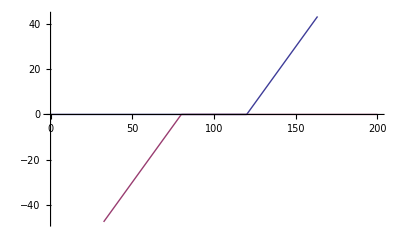

```mathematica
Plot[{OptionPayoff[MkOption[long, call, 120], S], OptionPayoff[MkOption[short, put, 80], S]}, {S, 0, 200}]
```

```mathematica
Manipulate[Plot[
PortfolioPayoff[{
MkOption[p1, t1, e1],
MkOption[p2, t2, e2]}, 
S], {S, 0, 200}, AxesOrigin->{0, 0}], 
"Option1",
Row[{
Control[{{p1, "long", ""}, {"long", "short"}}], 
Control[{{t1, "call", ""}, {"call", "put"}}], 
Control[{{e1, 80, ""}, 0, 200}],
Spacer[10],
Dynamic[e1]
}],
"Option 2",
Row[{
Control[{{p2, "short", ""},{"long", "short"}}],
Control[{{t2, "call", ""}, {"call", "put"}}],
Control[{{e2, 100, ""}, 0, 200}],
Spacer[10],
Dynamic[e2]
}]]
```

```mathematica
Manipulate[Plot[
PortfolioPayoff[{
MkOption[p1, t1, e1],
MkOption[p2, t2, e2],
MkOption[p3, t3, e3]}, 
S], {S, 0, 200}, AxesOrigin->{0, 0}], 
"Option1",
Row[{
Control[{{p1, "long", ""}, {"long", "short"}}], 
Control[{{t1, "call", ""}, {"call", "put"}}], 
Control[{{e1, 80, ""}, 0, 200}],
Spacer[10],
Dynamic[e1]
}],
"Option 2",
Row[{
Control[{{p2, "short", ""},{"long", "short"}}],
Control[{{t2, "call", ""}, {"call", "put"}}],
Control[{{e2, 100, ""}, 0, 200}],
Spacer[10],
Dynamic[e2]
}],
"Option 3",
Row[{
Control[{{p3, "short", ""},{"long", "short"}}],
Control[{{t3, "call", ""}, {"call", "put"}}],
Control[{{e3, 120, ""}, 0, 200}],
Spacer[10],
Dynamic[e3]
}]
]
```